```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.5, la->1.5};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
```

```mathematica
(*Locations of all the known ground joints*)
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];
```

```mathematica
al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
```

```mathematica
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
```

```mathematica
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
```

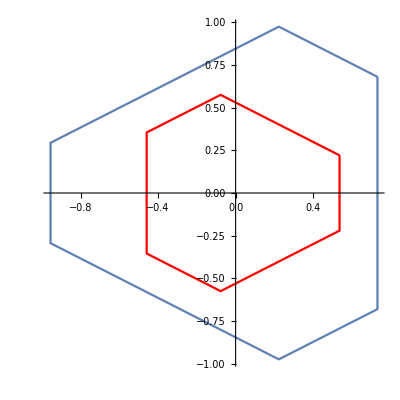

```mathematica
Show[ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]]],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Red], AspectRatio->1]
```

```mathematica
(*Variables*)
```

```mathematica
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
l = Table[Symbol["l"<>ToString[i]],{i,6}];
```

```mathematica
(*Assume the center of the top plate and the orientation as p and R*)
```

```mathematica
pc = {x, y, z};
qq = Join[ϕ, ψ, l];
qx = Join[pc, {c1, c2, c3}];
q = Join[qx, qq];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
```

```mathematica
(*Checking the orthogonolity of the rotation matrix*)
```

```mathematica
Simplify[Rtp.T[Rtp]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Jvtp = D[pc, {q}];
Jωtp = SkewMat2vec[Simplify[T[Rtp].D[Rtp,{q}]]];
```

```mathematica
(*Formulating the dynamics equations of the manipulator*)
```

```mathematica
(*Finding the Jvp for the ai parts of the links*)
```

```mathematica
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
```

```mathematica
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
```

```mathematica
Jpai = D[pa, {q}];
Jpbi = D[pb, {q}];
```

```mathematica
(*To generate the test data for this system*)
```

```mathematica
qqrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
qxrule = {x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]};
qrule = Join[qxrule,qqrule];
```

```mathematica
(*Angular velocity of any leg li*)
```

```mathematica
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
Jωl = Table[SkewMat2vec[T[Rl[[i]]].D[Rl[[i]],{q}]],{i, 6}];
```

```mathematica
(*Mass Matrix*)
```

```mathematica
tempM = Append[(Table[T[Jpai[[i]]].Jpai[[i]]*ma+T[Jpbi[[i]]].Jpbi[[i]]*mb+T[Jωl[[i]]].Ibi.Jωl[[i]]+T[Jωl[[i]]].Iai.Jωl[[i]],{i, 6}]), T[Jvtp].Jvtp*mtp+T[Jωtp].Itp.Jωtp];
tempM//dim
```

{7,24,24}

```mathematica
tempM2 = Total[tempM, {1}];
tempM2//dim
```

{24,24}

```mathematica
tempM2 - T[tempM2]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
tempM2//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,la,lb,ma,mb,mtp,ri,ro,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
Mmat = Simplify[tempM2/.qrule/.datap/.leglparam/.legmparam/.tpmparam];
```

```mathematica
Mmat//Variables
```

{c1[t],c2[t],c3[t],Cos[2 ψ1[t]],Cos[2 ψ2[t]],Cos[2 ψ3[t]],Cos[2 ψ4[t]],Cos[2 ψ5[t]],Cos[2 ψ6[t]],l1[t],l2[t],l3[t],l4[t],l5[t],l6[t]}

```mathematica
size[Mmat]
```

Size of the expression is:32.0391 KB.

```mathematica
qt = q/.qrule;
```

```mathematica
tic[]
n = Length[qt];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii= 1, ii≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[Mmat[[ii,jj]], qt[[kk]]] + D[Mmat[[ii,kk]], qt[[jj]]] - D[Mmat[[jj, kk]], qt[[ii]]])*D[qt[[kk]],t] ;
kk++];
jj++];
ii++];
toc[]
```

Actual time consumed: 0.18349 seconds.

CPU time consumed: 0.18367 seconds.

```mathematica
sampledat = {ϕ1[t]->-0.4120776809584599,ϕ2[t]->-0.5171397464399574,ϕ3[t]->0.17764187369764603,ϕ4[t]->0.28736859806179627,ϕ5[t]->0.19195198975076458,ϕ6[t]->0.3314663928113124,ψ1[t]->-0.010571279864228872,ψ2[t]->0.00656986783518712,ψ3[t]->0.2888385292898862,ψ4[t]->0.45146664507018724,ψ5[t]->-0.32862234369207344,ψ6[t]->-0.5474095601531795,l1[t]->1.0763732914509816,l2[t]->1.3589653226424672,l3[t]->1.3306253991320864,l4[t]->1.3670902994040683,l5[t]->1.1391099344974789,l6[t]->1.163106217592093};
```

```mathematica
initvel = {ϕ1'[t]->0.04819125830959889,ϕ2'[t]->0.03427428403166,ϕ3'[t]->0.022537110420045366,ϕ4'[t]->-0.02504333390626954,ϕ5'[t]->-0.06015570745871055,ϕ6'[t]->-0.06962346394226754,ψ1'[t]->0.17522543152669445,ψ2'[t]->0.09442759444255354,ψ3'[t]->0.05971195202706652,ψ4'[t]->0.04189876317323693,ψ5'[t]->0.08197436457283205,ψ6'[t]->0.1734108446847269,l1'[t]->0.1,l2'[t]->0,l3'[t]->0,l4'[t]->0,l5'[t]->0,l6'[t]->0};
```

```mathematica
Mmatdat = D[Mmat, t];
tempA = Mmatdat-2*tempC;
temppA = tempA+T[tempA];
temppA//dim
Chop[Simplify[temppA]]
```

{24,24}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*Formulating the potential term*)
```

```mathematica
tempV = Table[{ma*g*pa[[i]][[3]], mb*g*pb[[i]][[3]]},{i, 6}];
```

```mathematica
V = Total[Append[Flatten[tempV], mtp*g*pc[[3]]]]/.datap/.leglparam/.legmparam/.tpmparam;
G = D[V, {q}];
```

```mathematica
Variables[G]
```

{l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
(*Now we have dynamics in the extended configuration space. We need to map it back to the task space of the manipulator*)
```

```mathematica
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating the simple constraint equations (not the rigidity of the top platform constraint)*)
```

```mathematica
η = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
η//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,x,y,z,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
η//Dimensions
```

{18}

```mathematica
η/.Inner[Rule, q, Join[{0,0,1.1,0,0,0}, iksol[{0,0,1.1,0,0,0}]], List]
```

{-5.55112×10^-17,-5.55112×10^-17,0.,0.,-1.66533×10^-16,-2.22045×10^-16,5.55112×10^-17,6.93889×10^-18,0.,2.77556×10^-16,1.59595×10^-16,0.,-5.55112×10^-17,5.55112×10^-17,0.,1.11022×10^-16,-5.55112×10^-17,0.}

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}];(*s is tan ψ/2*)
```

```mathematica
lsample = Inner[Rule, l, iksol[{0,0,1.1,0,0,0}][[-6;;]], List]
```

{l1→1.20833,l2→1.20833,l3→1.20833,l4→1.20833,l5→1.20833,l6→1.20833}

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
Denominator[Together[η/.lsample/.htanrule]]
```

{(1.+c1^2+c2^2+c3^2) (1.+p1^2) (1.+s1^2),(1.+c1^2+c2^2+c3^2) (1.+s1^2),(1.+c1^2+c2^2+c3^2) (1.+p1^2) (1.+s1^2),(1.+c1^2+c2^2+c3^2) (1.+p2^2) (1.+s2^2),(1.+c1^2+c2^2+c3^2) (1.+s2^2),(1.+c1^2+c2^2+c3^2) (1.+p2^2) (1.+s2^2),(1.+c1^2+c2^2+c3^2) (1.+p3^2) (1.+s3^2),(1.+c1^2+c2^2+c3^2) (1.+s3^2),(1.+c1^2+c2^2+c3^2) (1.+p3^2) (1.+s3^2),(1.+c1^2+c2^2+c3^2) (1.+p4^2) (1.+s4^2),(1.+c1^2+c2^2+c3^2) (1.+s4^2),(1.+c1^2+c2^2+c3^2) (1.+p4^2) (1.+s4^2),(1.+c1^2+c2^2+c3^2) (1.+p5^2) (1.+s5^2),(1.+c1^2+c2^2+c3^2) (1.+s5^2),(1.+c1^2+c2^2+c3^2) (1.+p5^2) (1.+s5^2),(1.+c1^2+c2^2+c3^2) (1.+p6^2) (1.+s6^2),(1.+c1^2+c2^2+c3^2) (1.+s6^2),(1.+c1^2+c2^2+c3^2) (1.+p6^2) (1.+s6^2)}

```mathematica
ηlist = Numerator[Together[η/.lsample/.htanrule]];
```

```mathematica
ηlist[[18]]//Simplify
```

1.2083279353106968 + 1.2083279353106968*c3^2 - 1.2083279353106968*p6^2 - 1.2083279353106968*c3^2*p6^2 - 1.2083279353106968*s6^2 - 
  1.2083279353106968*c3^2*s6^2 + 1.2083279353106968*p6^2*s6^2 + 1.2083279353106968*c3^2*p6^2*s6^2 + 
  c1*(0.44113669866436045 + 0.44113669866436045*s6^2 + p6^2*(0.44113669866436045 + 0.44113669866436045*s6^2) + 
    c3*(-1.073494654430803 - 1.073494654430803*s6^2 + p6^2*(-1.073494654430803 - 1.073494654430803*s6^2))) + 
  c2*(1.073494654430803 + 1.073494654430803*s6^2 + p6^2*(1.073494654430803 + 1.073494654430803*s6^2) + 
    c3*(0.44113669866436045 + 0.44113669866436045*s6^2 + p6^2*(0.44113669866436045 + 0.44113669866436045*s6^2))) + 
  c1^2*(1.2083279353106968 + s6^2*(-1.2083279353106968 - 1.*z) + p6^2*(-1.2083279353106968 + s6^2*(1.2083279353106968 - 1.*z) - 1.*z) - 
    1.*z) + c2^2*(1.2083279353106968 + s6^2*(-1.2083279353106968 - 1.*z) + 
    p6^2*(-1.2083279353106968 + s6^2*(1.2083279353106968 - 1.*z) - 1.*z) - 1.*z) - 1.*z - 1.*c3^2*z - 1.*p6^2*z - 1.*c3^2*p6^2*z - 1.*s6^2*z - 
  1.*c3^2*s6^2*z - 1.*p6^2*s6^2*z - 1.*c3^2*p6^2*s6^2*z

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
(*ηleg = Table[Together[((atps-b)[[i]]).((atp-b)[[i]])-l[[i]]^2],{i, 6}];*)
```

```mathematica
(*ηtask = Join[η, ηleg]/.alsrules/.bsrules/.datap;*)
```

```mathematica
(*ηtask//Dimensions
ηtask//Variables*)
```

```mathematica
Jηq = D[η, {qq}];
Jηx =D[η, {qx}];
```

```mathematica
(*Assuming the working of the manipulator in SWZ and also not having Jηq singularity anywhere. Interesting that this map demands Jηq Jacobians existence and not Jηϕ*)
```

```mathematica
(*Since the matrix is sparse, try symbolic inverse some other time*)
```

```mathematica
dϕ = Table[Symbol["dϕ"<>ToString[i]],{i, 6}];
dψ = Table[Symbol["dψ"<>ToString[i]],{i, 6}];
dl = Table[Symbol["dl"<>ToString[i]],{i, 6}];
dq = Join[dϕ, dψ,dl];
dqrule = Inner[Rule, D[qq/.qrule, t], dq, List];
rqϕrule= Join[Inner[Rule,qq/.qrule, qq, List], dqrule];
rxrule = Inner[Rule, qx/.qrule, qx, List];
drxrule = Inner[Rule, D[qx/.qrule, t], {dx, dy, dz, dc1, dc2, dc3}, List];
rqrule = Join[rxrule, drxrule, rqϕrule];
```

```mathematica
cJηq = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Jηq]];
```

```mathematica
dJηq = D[Jηq/.qrule, t]/.rqrule;
cdJηq = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηq]];
```

```mathematica
cJηx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Jηx]];
```

```mathematica
dJηx = D[Jηx/.qrule, t]/.rqrule;
cdJηx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηx]];
```

```mathematica
tMmat = TrigExpand[Mmat/.rqrule];
cMmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tMmat]];
```

```mathematica
tCmat = TrigExpand[Simplify[tempC/.rqrule]];
cCmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[tCmat]];
```

```mathematica
cGvec = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[G]];
```

```mathematica
(*IK module for the manipulator*)
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksol[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
trigrules = (Join[sinϕrule/.Inner[Rule, Cos[ψ], cosψ, List]/.lirule/.bsrules/.alsrules/.datap, cosϕrule/.Inner[Rule, Cos[ψ], cosψ, List]/.lirule/.bsrules/.alsrules/.datap, sinψrule/.lirule/.bsrules/.alsrules/.datap, cosψrule/.lirule/.bsrules/.alsrules/.datap, lirule/.bsrules/.datap]);
```

```mathematica
qsample = Join[{0,0,1.1,0,0,0}, iksol[{0,0,1.1,0,0,0}]];
```

```mathematica
(*Convert the equations to polynomial form to find the solutions using bertini*)
```

```mathematica
η//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,x,y,z,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
p = Table[Symbol["p"<>ToString[i]],{i,6}]; (*p is tan ϕ/2*)
s = Table[Symbol["s"<>ToString[i]],{i,6}];(*s is tan ψ/2*)
```

```mathematica
htanrule = Flatten[Table[{Cos[ϕ[[i]]]->(1-p[[i]]^2)/(1+p[[i]]^2),Sin[ϕ[[i]]]->(2*p[[i]])/(1+p[[i]]^2), Cos[ψ[[i]]]->(1-s[[i]]^2)/(1+s[[i]]^2),Sin[ψ[[i]]]->(2*s[[i]])/(1+s[[i]]^2) },{i,6}]];
```

```mathematica
(*Make sure the denominator is not zero*)
```

```mathematica
Denominator[Together[η/.htanrule]]
```

{(1.+c1^2+c2^2+c3^2) (1.+p1^2) (1.+s1^2),(1.+c1^2+c2^2+c3^2) (1.+s1^2),(1.+c1^2+c2^2+c3^2) (1.+p1^2) (1.+s1^2),(1.+c1^2+c2^2+c3^2) (1.+p2^2) (1.+s2^2),(1.+c1^2+c2^2+c3^2) (1.+s2^2),(1.+c1^2+c2^2+c3^2) (1.+p2^2) (1.+s2^2),(1.+c1^2+c2^2+c3^2) (1.+p3^2) (1.+s3^2),(1.+c1^2+c2^2+c3^2) (1.+s3^2),(1.+c1^2+c2^2+c3^2) (1.+p3^2) (1.+s3^2),(1.+c1^2+c2^2+c3^2) (1.+p4^2) (1.+s4^2),(1.+c1^2+c2^2+c3^2) (1.+s4^2),(1.+c1^2+c2^2+c3^2) (1.+p4^2) (1.+s4^2),(1.+c1^2+c2^2+c3^2) (1.+p5^2) (1.+s5^2),(1.+c1^2+c2^2+c3^2) (1.+s5^2),(1.+c1^2+c2^2+c3^2) (1.+p5^2) (1.+s5^2),(1.+c1^2+c2^2+c3^2) (1.+p6^2) (1.+s6^2),(1.+c1^2+c2^2+c3^2) (1.+s6^2),(1.+c1^2+c2^2+c3^2) (1.+p6^2) (1.+s6^2)}

```mathematica
ηpoly = Expand[Numerator[Together[η/.htanrule]]];
```

```mathematica
ηpolylist = Expand[Numerator[Together[η/.Inner[Rule, q[[-6;;]], qsample[[-6;;]], List]/.htanrule]]];
```

```mathematica
(*Convert equations to input form to make them bertini compatible*)
```

```mathematica
(*Check if using real numbers is a good idea for bertini*)
```

```mathematica
ηpolylist[[1]]
```

0.195829+0.195829 c1^2-0.441137 c1 c2+1.26932 c2^2+0.441137 c3+1.26932 c3^2+2.41666 p1+2.41666 c1^2 p1+2.41666 c2^2 p1+2.41666 c3^2 p1+0.195829 p1^2+0.195829 c1^2 p1^2-0.441137 c1 c2 p1^2+1.26932 c2^2 p1^2+0.441137 c3 p1^2+1.26932 c3^2 p1^2+0.195829 s1^2+0.195829 c1^2 s1^2-0.441137 c1 c2 s1^2+1.26932 c2^2 s1^2+0.441137 c3 s1^2+1.26932 c3^2 s1^2-2.41666 p1 s1^2-2.41666 c1^2 p1 s1^2-2.41666 c2^2 p1 s1^2-2.41666 c3^2 p1 s1^2+0.195829 p1^2 s1^2+0.195829 c1^2 p1^2 s1^2-0.441137 c1 c2 p1^2 s1^2+1.26932 c2^2 p1^2 s1^2+0.441137 c3 p1^2 s1^2+1.26932 c3^2 p1^2 s1^2-1. x-1. c1^2 x-1. c2^2 x-1. c3^2 x-1. p1^2 x-1. c1^2 p1^2 x-1. c2^2 p1^2 x-1. c3^2 p1^2 x-1. s1^2 x-1. c1^2 s1^2 x-1. c2^2 s1^2 x-1. c3^2 s1^2 x-1. p1^2 s1^2 x-1. c1^2 p1^2 s1^2 x-1. c2^2 p1^2 s1^2 x-1. c3^2 p1^2 s1^2 x

```mathematica
doubledots[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval, LHS, Jηqval, Jηxval, Jqexval, Mxval, dMmatval, Cxval, Gxval, dJηxval, dJηqval, dJqexval, Jqxval, dqe, qe},
(*Perform the IK for the configuration variables*)
qe = Join[q, iksol[q]];
(*qe = Join[q, ciksol@@q];*)
(*Getting the velocities of the configuration space variables*)
Jηqval = cJηq@@qe;
Jηxval = cJηx@@qe;
Jqxval = -Inverse[Jηqval].Jηxval;
dqe = Join[dq, Jqxval.dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηqval = cdJηq@@Join[qe, dqe];
dJηxval = cdJηx@@Join[qe, dqe];
(*Map of the matrices*)
Jqexval = ArrayFlatten[{{IdentityMatrix[6]}, {Jqxval}}];
dJqexval = ArrayFlatten[{{ConstantArray[0,{6,6}]}, {-Inverse[Jηqval].(-dJηqval.Inverse[Jηqval].Jηxval+dJηxval)}}];
(*Map the matrices to the task space*)
Mxval = T[Jqexval].Mval.Jqexval;
Cxval = T[Jqexval].(Mval.dJqexval+Cval.Jqexval);
Gxval = T[Jqexval].Gval;
(*LHS of the dynamics equations*)
LHS = -(Inverse[Mxval]).(Cxval.dq+Gxval);
Return[LHS];
];
```

```mathematica
qval = {0,0,1.1,0,0,0};
dqval = {0,0,0,0,0,0};
```

```mathematica
(*There is some problem with finding the velocity of the configuration space variables from the task space velocities*)
```

```mathematica
tic[]
dynsim = NDSolve[{doubledots[q1[t],q1'[t]]==q1''[t],q1[0]==qval,q1'[0]==dqval},q1,{t,0,1},Method->"Adams", AccuracyGoal->15]
toc[]
```

{{q1→InterpolatingFunction[…]}}

Actual time consumed: 0.827125 seconds.

CPU time consumed: 0.297 seconds.

```mathematica
(*loop closure in completely task space variables*)
ηeqn = η/.trigrules/.datap/.leglparam/.legmparam/.tpmparam;
```

```mathematica
(*Now performing the energy checks needed*)
```

```mathematica
qsol = (q1/.dynsim)[[1]];
```

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize, PlotRange->All];

Return[f1nonsing];
]
```

```mathematica
(*1. Zeroth order check: Checking the norm of the loop closure througout the motion*)
```

```mathematica
time = Table[t, {t, 0, 1, 0.01}];
```

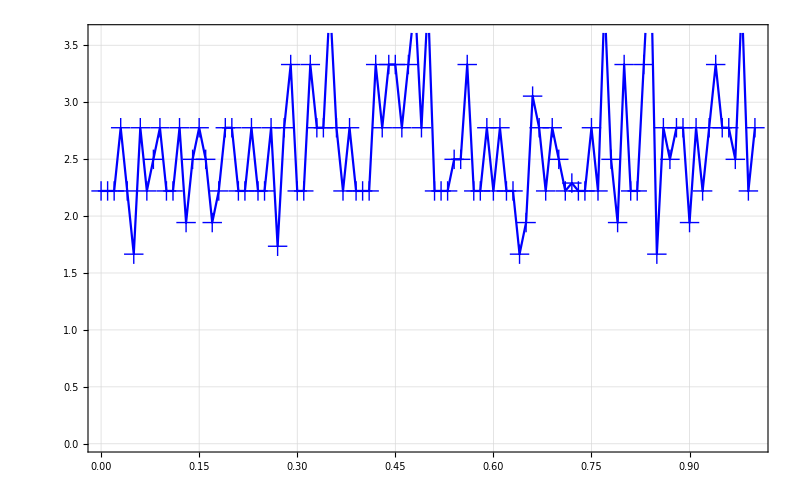

```mathematica
ηtest = Table[Max[Abs[ηeqn/.Inner[Rule,qx,qsol[i], List]]],{i, 0, 1, 0.01}];
Texplot[time, ηtest*10^16, 800, "Time~(s)", "e_1 (\\times 10^{-16})"]
```

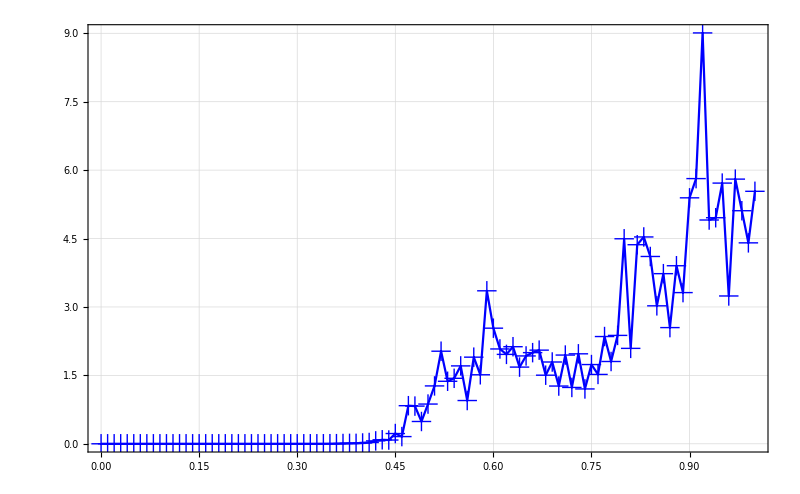

```mathematica
(*2. First order check: Checking the norm of Jηq.q' check*)
Jηeqnx = D[ηeqn, {qx}];
cJηeqnx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[Jηeqnx]];
Jηeqnxtest = Table[Max[Abs[cJηeqnx@@qsol[i].qsol'[i]]],{i, 0, 1, 0.01}];
Texplot[time, Jηeqnxtest*10^21, 800, "Time~(s)", "e_2 (\\times 10^{-21})"]
```

```mathematica
(*3. Second order check: Cheking norm of Jηq.d2q+dJηq.dq*)
dJηeqnx = D[Jηeqnx/.qrule, t];
dJηeqnx2 = dJηeqnx/.rqrule;
```

```mathematica
cdJηeqnx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}}, Evaluate[dJηeqnx2]];
```

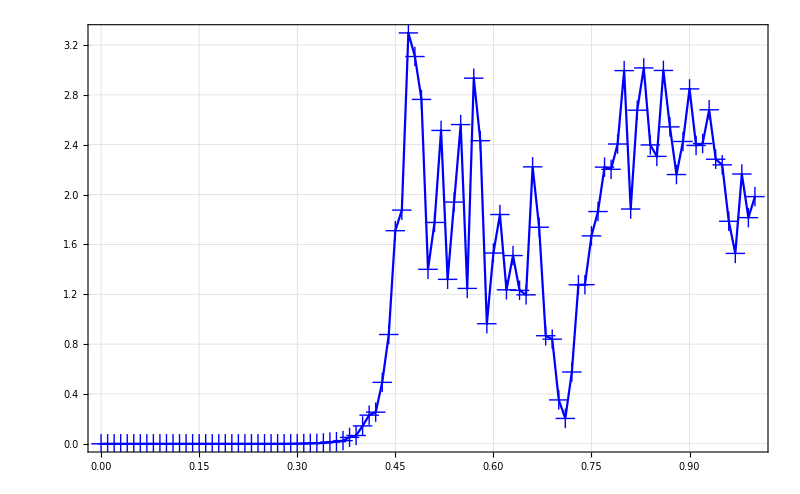

```mathematica
dJηeqnxtest = Table[Norm[cJηeqnx@@qsol[i].qsol''[i]+cdJηeqnx@@Join[qsol[i], qsol'[i]].qsol'[i]],{i, 0, 1, 0.01}];
Texplot[time, dJηeqnxtest*10^20, 800, "Time~(s)", "e_3 (\\times 10^{-20})"]
```

```mathematica
(*To check Energy remove the applied external torque*)
(*4. Energy: Checking Energy constant criteria*)
Vsubs = V/.trigrules/.bsrules/.alsrules/.datap/.leglparam/.legmparam/.tpmparam;
Msubs = TrigExpand[Mmat]/.rqrule/.trigrules/.bsrules/.alsrules/.datap/.leglparam/.legmparam/.tpmparam;
Vlist = Table[Vsubs/.Inner[Rule,qx, qsol[i], List], {i, 0, 1, 0.01}];
Mlist = Table[Msubs/.Inner[Rule,qx, qsol[i], List], {i, 0, 1, 0.01}];
qfull = Table[Join[qsol[i], iksol[qsol[i]]],{i, 0, 1, 0.01}];
```

```mathematica
Jηqtab = Table[cJηq@@qfull[[i]],{i, Length[qfull]}];
Jηxtab = Table[cJηx@@qfull[[i]],{i, Length[qfull]}];
```

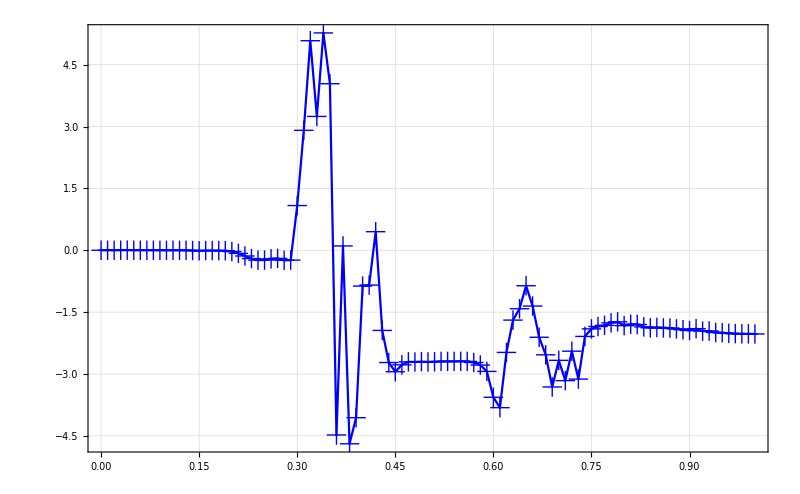

```mathematica
Jqxtab = Table[-Inverse[Jηqtab[[i]]].Jηxtab[[i]], {i, Length[qfull]}];
dq2 = Table[qsol'[i], {i, 0, 1, 0.01}];
dqtab = Table[Join[dq2[[i]], Jqxtab[[i]].dq2[[i]]],{i, Length[dq2]}];
Hlist = Table[1/2*(dqtab[[i]].Mlist[[i]].dqtab[[i]])+Vlist[[i]],{i, Length[dq2]}];
H1 = ConstantArray[Hlist[[1]], Dimensions[Hlist]];
Texplot[time,(Hlist-H1)/H1*10^8, 800, "Time~(s)", "e_3 (\\times 10^{-8})"]
```

```mathematica
qvals = Table[Inner[Rule, q, Join[qsol[i],iksol[qsol[i]]], List],{i, 0,1, 0.001}];
```

```mathematica
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
```

```mathematica
(*plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.3, 1.3}, {-1.3, 1.3}, {-1.3, 1.3}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
(*llinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],aval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
lainks = Table[Graphics3D[{LightOrange,Opacity[0.5],Cylinder[{aval[[i]]/.qvals, bval[[i]]+direction[[i]]*(lb)/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
(*Plotting the configuration*)
Show[base, top, jointstop, jointsbase, lainks, lbinks]]*)
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.3, 1.3}, {-1.3, 1.3}, {-1.3, 1.3}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
(*llinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],aval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
lainks = Table[Graphics3D[{LightOrange,Opacity[0.5],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
(*Plotting the configuration*)
Show[base, top, jointstop, jointsbase, lainks, lbinks]]
```

```mathematica
testpose = Inner[Rule, q, Join[{-0.2,0.1,1,0,0,-0.2}, iksol[{-0.2,0.1,1,0,0,-0.2}]], List]
```

{x→-0.2,y→0.1,z→1,c1→0,c2→0,c3→-0.2,ϕ1→-0.338707,ϕ2→-0.266885,ϕ3→0.437797,ϕ4→0.192929,ϕ5→-0.621257,ϕ6→-0.481054,ψ1→0.503129,ψ2→0.294223,ψ3→-0.273617,ψ4→-0.234579,ψ5→-0.436455,ψ6→-0.317464,l1→1.21021,l2→1.08325,l3→1.14679,l4→1.0476,l5→1.357,l6→1.18735}

```mathematica
(*plotsrspm[testpose]*)
```

```mathematica
(*Export["image.pdf",image,ImageResolution->600]*)
```

```mathematica
mansrspm = Manipulate[
plotsrspm[qvals[[j]]],
{j, 1, Length[qvals], 1}, ContentSize->{400,400}]
```

```mathematica
(*t=0*)
```

```mathematica
(*Show[plotsrspm[qvals[[480]]],ImageResolution->600]*)
```

```mathematica
(*frames = Table[Export["etask"<>ToString[j/4]<>".jpeg", plotsrspm[qvals[[j]]]],{j, 4, 824, 4}];*)
```

```mathematica
(*Writing a general function to take any Mathematica expression into a C compatible file or into a template file*)
```

```mathematica
trigrep[i_]:={Cos[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[lambda]<>ToString[i]]],Sin[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[mu]<>ToString[i]]],Sec[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]]),Csc[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]),Tan[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[mu]<>ToString[i]]])/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]])),Cot[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[lambda]<>ToString[i]]])/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]))};
alpharep[i_]:={ToExpression[Symbol[ToString[α]<>ToString[i]]]-> ToExpression[Symbol[ToString[alpha]<>ToString[i]]]};
alpharepall=Union[alpharep[1],alpharep[2],alpharep[3],alpharep[4],alpharep[5],alpharep[6]];
revtrigrep[i_]:=Reverse[trigrep[i],2];
trigrepall=Union[trigrep[1],trigrep[2],trigrep[3],trigrep[4],trigrep[5],trigrep[6]];
revtrigrepall=Union[revtrigrep[1],revtrigrep[2],revtrigrep[3],revtrigrep[4],revtrigrep[5],revtrigrep[6]];
revreplist=Reverse[replist,2];
revalpharepall=Reverse[alpharepall,2];
inversetrig =  Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
replist=Union[{Power-> pow},trigrepall,{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]}];
Print["Change the angles from Greek symbols"]
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[replist,2].

Change the angles from Greek symbols

```mathematica
phi = Table[Symbol["p"<>ToString[i]],{i, 6}];
psi = Table[Symbol["s"<>ToString[i]],{i, 6}];
dphi = Table[Symbol["dp"<>ToString[i]],{i, 6}];
dpsi = Table[Symbol["ds"<>ToString[i]],{i, 6}];
nogreek = Join[Inner[Rule, ϕ, phi, List], Inner[Rule, ψ, psi, List], Inner[Rule, dϕ, dphi, List], Inner[Rule, dψ, dpsi, List]];
```

```mathematica
cospsi = Table[Symbol["cs"<>ToString[i]],{i, 6}];
sinpsi = Table[Symbol["ss"<>ToString[i]],{i, 6}];
cosphi = Table[Symbol["cp"<>ToString[i]],{i, 6}];
sinphi = Table[Symbol["sp"<>ToString[i]],{i, 6}];
```

```mathematica
trigtoalg = Join[Inner[Rule, Cos[ψ], cospsi, List], Inner[Rule, Sin[ψ], sinpsi, List], Inner[Rule, Cos[ϕ], cosphi, List], Inner[Rule, Sin[ϕ], sinphi, List]];
```

```mathematica
(*Exporting the matrices to C++*)
```

```mathematica
PortMattoC[mat_]:=Module[{tempMattoC, mattoC},
(*Substitute all Greek letters and flatten matrices into vectors*)
tempMattoC = Flatten[mat]/.trigtoalg/.replist/.inversetrig/.nogreek;
mattoC  = StringTake[ToString[Table[CForm[tempMattoC[[i]]],{i, Length[tempMattoC]}]],{2,-2}];
Return [mattoC];
]
```

```mathematica
redrule = Inner[Rule, {cos[2 s1], cos[2 s2],cos[2 s3],cos[2 s4], cos[2 s5],cos[2 s6]}, {cs21, cs22, cs23, cs24, cs25, cs26}, List];
```

```mathematica
tMmat2 = Simplify[tMmat]/.trigtoalg/.replist/.nogreek/.redrule/.inversetrig;
```

```mathematica
MmattoC = PortMattoC[tMmat2];
CmattoC = PortMattoC[tCmat];
GmattoC = PortMattoC[G];
```

```mathematica
JηqqtoC = PortMattoC[Jηq];
JηqxtoC = PortMattoC[Jηx];
```

```mathematica
dJηqqtoC = PortMattoC[dJηq];
dJηqxtoC = PortMattoC[dJηx];
```

```mathematica
lvaltoc = PortMattoC[l/.lval];
ϕvaltoc = PortMattoC[ϕ/.ϕval];
ψvaltoc = PortMattoC[ψ/.ψval];
```

```mathematica
file = Import["dyn_funcs.h", "Text"];
```

```mathematica
FileTemplateApply[file,<|"Mexpressions1"->MmattoC, "Cexpressions1"->CmattoC, "Gexpressions1"->GmattoC,"Jetaqphiexpressions1"->JηqqtoC, "Jetaqxexpressions1"->JηqxtoC, "dJetaqphiexpressions1"->dJηqqtoC, "dJetaqxexpressions1"->dJηqxtoC, "lexpressions1"->lvaltoc, "phiexpressions1"->ϕvaltoc, "psiexpressions1"->ψvaltoc|>, "CPP/dyn_funcs_test.h"];
```

```mathematica
(*Jηl = D[η, {q[[-6;;]]}];*)
```

```mathematica
(*Jηϕe = D[η, {q[[;;-7]]}];*)
```

```mathematica
(*vels = Inverse[Jηϕe/.testpose].(Jηl/.testpose).{0.1,0,0,0,0,0}*)
```

```mathematica
(*fullvel = Join[vels, {0.1,0,0,0,0,0}];*)
```

```mathematica
(*dfullq = Join[{dx, dy, dz, dc1, dc2, dc3},dq]*)
```

```mathematica
(*fullvel  = Inner[Rule, dfullq, fullvel, List]*)
```

```mathematica
(*testpose*)
```

```mathematica
(*PortMattoC[dJηx/.testpose/.fullvel]*)
```